```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../Models/SMS-stop-FA/SMS-stop-FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

## g g → t t (1-loop)

```mathematica
tops0 = CreateTopologies[0,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}]; 
tops = CreateTopologies[1,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT =  { V[4],V[4]} -> {F[9],-F[9]};
allDiags = InsertFields[Join[tops0,tops],processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[3],V[1],S[1],S[2],S[3],V[2],F[1],F[2],F[3],F[4],F[5],F[6],F[7],F[8]}];
```

generic model {Lorentz} initialized

classes model {../../Models/SMS-stop-FA/SMS-stop-FA} initialized

in total: 47 Particles insertions

```mathematica
amp=FCFAConvert[CreateFeynAmp[allDiags,PreFactor->1,Truncated->False]/.{SUNT->FASUNT},IncomingMomenta->{k1,k2},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->True,DropSumOver->True,SMP->True,LorentzIndexNames-> {μ,ν},Contract->True,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings//.{GS->gs}),ChangeDimension->D]/.{GS->gs};
nonZero={};
(* Keep only the diagrams up to gs^2 and containing yDM *)
For[n=1,n≤Length[amp],++n,
	M = Take[amp,{n}];
	M = SUNSimplify[M];
	M=Normal[Series[M,{gs,0,2}]];
	M=Normal[Series[M,{yDM,0,2}]];
	M=DiracSimplify[M];
    If[!M==={0} && !FreeQ[M,yDM] ,AppendTo[nonZero,n]];
];
```

in total: 47 Particles amplitudes

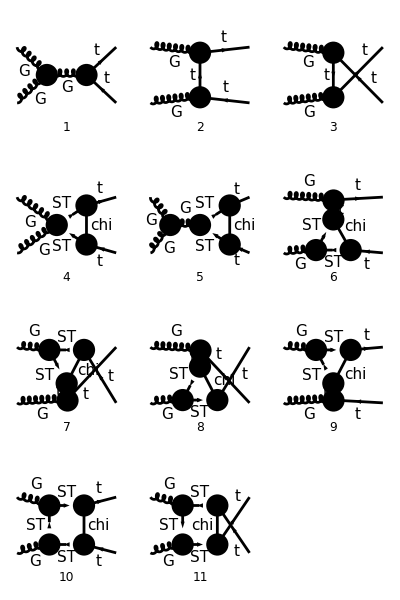

```mathematica
goodDiags=DiagramExtract[allDiags,nonZero];
(* goodDiags=DiagramExtract[goodDiags,{5}]; *)
Paint[goodDiags,ColumnsXRows->{3,4},ImageSize->{ 400,600},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->False]/.{SUNT->FASUNT},IncomingMomenta->{k1,k2},OutgoingMomenta->{p1,p2},TransversePolarizationVectors->{k1,k2}, LoopMomenta->{q},List->False,DropSumOver->True,SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs};
ampB =Simplify[SUNSimplify[DiracSimplify[ampA]]]
```

in total: 11 Particles amplitudes

gs^2 (-(4 ⅈ deltaCTL^2 MT π^4 yDM^4 (φ(p1,MT)).(γ·ε(k1)).(γ·ε(k2)).(γ̄)^6.(φ(-p2,MT)) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)+301+(2 deltaCTR π^2 yDM^2+1) 1 (((k1·ε(k2)+p1·ε(k2)+p2·ε(k2)) f^1 T_1^Glu5)/(p1+p2)^2+1/1+(2 (1-1) 1)/(1^2-MT^2)))
 |  |  |  |

```mathematica
ampC =( TID[ampB,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True]//Simplify);
```

```mathematica
(* Remove SM contribution *)
ampSM=gs^2 SeriesCoefficient[ampC,{gs,0,2},{yDM,0,0}];
ampC=Simplify[ampC-ampSM];
```

## On - Shell Case :

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,MT,MT,0,0];
```

```mathematica
ampEsimp=Simplify[DiracSimplify[ampC]]
```

(ⅈ gs^2 π^2 yDM^2 (t u (-(4 5 (11)_Col3Col4)/((1)^2-MT^2)+837+1+1 (1))+1 1))/(t u)
 |  |  |  |

```mathematica
ampEsimp2=Simplify[DotSimplify[DiracSimplify[ampEsimp,DiracSubstitute67->True]]]
```

(ⅈ 3 (t u (1079+(φ(p1,MT)).(γ·1).(1) 1)+1-(φ(p1,MT)).(γ·1).1.(φ(-p2,MT)) 1))/(2 t u)
 |  |  |  |

```mathematica
sps=Cases2[ampEsimp2,Spinor]
moms=Cases2[ampEsimp2,DiracGamma]
pairs=Cases2[ampEsimp2,Pair]
```

{φ(p1,MT),φ(-p2,MT)}

{(γ̄)^5,γ·k1,γ·k2,γ·ε(k1),γ·ε(k2)}

{k1·ε(k2),k2·ε(k1),p1·ε(k1),p1·ε(k2),p2·ε(k1),p2·ε(k2),ε(k1)·ε(k2)}

```mathematica
terms = Table[Simplify[DiracSimplify[Coefficient[ampEsimp2,pairs[[i]]],DiracSubstitute5->True]],{i,1,Length[pairs]}];
```

```mathematica
Collect[DiracSimplify[DiracSimplify[FCReplaceMomenta[terms[[-1]]/.{DiracGamma[7]->1-DiracGamma[6]},{k1->p1+p2-k2}]]/.{DiracGamma[7]->1-DiracGamma[6]}],{SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu5]]},FullSimplify]
```

1/(p1+p2)^2 gs^2 π^2 yDM^2 (4 (deltaCTL (φ(p1,MT)).(γ·k2).(φ(-p2,MT))+MT (φ(p1,MT)).(γ̄)^6.(φ(-p2,MT)) (deltaCTL-deltaCTR-C_00(MT^2,s,MT^2,mChi^2,mST^2,mST^2))+(φ(p1,MT)).(γ·k2).(γ̄)^6.(φ(-p2,MT)) (-deltaCTL+deltaCTR+C_00(MT^2,s,MT^2,mChi^2,mST^2,mST^2)))+MT (φ(p1,MT)).(φ(-p2,MT)) (2 (-deltaCTL+deltaCTR+C_00(MT^2,s,MT^2,mChi^2,mST^2,mST^2))+(t-u) (C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+C_11(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+C_12(MT^2,s,MT^2,mChi^2,mST^2,mST^2)))) f^Glu1Glu2Glu5 T_Col3Col4^Glu5-ⅈ gs^2 π^2 yDM^2 (4 (φ(p1,MT)).(γ·k2).(γ̄)^6.(φ(-p2,MT)) (D_001(0,u,MT^2,s,MT^2,-2 MT^2+s+t+u,mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-D_001(0,t,MT^2,s,MT^2,-2 MT^2+s+t+u,mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4)+4 MT (φ(p1,MT)).(γ̄)^6.(φ(-p2,MT)) ((D_00(0,u,MT^2,s,MT^2,-2 MT^2+s+t+u,mST^2,mST^2,mChi^2,mST^2)+D_002(0,u,MT^2,s,MT^2,-2 MT^2+s+t+u,mST^2,mST^2,mChi^2,mST^2)+2 D_003(0,u,MT^2,s,MT^2,-2 MT^2+s+t+u,mST^2,mST^2,mChi^2,mST^2)) (T^Glu2 T^Glu1)_Col3Col4-(D_00(0,t,MT^2,s,MT^2,-2 MT^2+s+t+u,mST^2,mST^2,mChi^2,mST^2)+D_002(0,t,MT^2,s,MT^2,-2 MT^2+s+t+u,mST^2,mST^2,mChi^2,mST^2)+2 D_003(0,t,MT^2,s,MT^2,-2 MT^2+s+t+u,mST^2,mST^2,mChi^2,mST^2)) (T^Glu1 T^Glu2)_Col3Col4)+MT (φ(p1,MT)).(φ(-p2,MT)) (4 (D_00(0,t,MT^2,s,MT^2,-2 MT^2+s+t+u,mST^2,mST^2,mChi^2,mST^2)+D_002(0,t,MT^2,s,MT^2,-2 MT^2+s+t+u,mST^2,mST^2,mChi^2,mST^2)+D_003(0,t,MT^2,s,MT^2,-2 MT^2+s+t+u,mST^2,mST^2,mChi^2,mST^2)) (T^Glu1 T^Glu2)_Col3Col4-4 D_003(0,u,MT^2,s,MT^2,-2 MT^2+s+t+u,mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2) ((T^Glu1 T^Glu2)_Col3Col4+(T^Glu2 T^Glu1)_Col3Col4)))

```mathematica
(* phi(k1).p1slash.phi(-k2) + phi(k1).p2slash.phi(-k2) = phi(k1).(p1slash+p2slash).phi(-k2) = phi(k1).(k1slash+k2slash).phi(-k2) = 0 *)
ampEsimp3=Collect[ampEsimp2,{sps[[3]].moms[[1]].sps[[4]]},Simplify]/.{sps[[2]].moms[[3]].sps[[1]]+sps[[2]].moms[[4]].sps[[1]]->0}
```

-1/(p1+p2)^2 ⅈ π^2 gs^2 yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 ((φ(-k2)).γ^μ.(φ(k1)) ((C00-deltaCTL+deltaCTR) (φ(p1,MT)).γ^μ.(γ̄)^5.(φ(-p2,MT))+(C00+deltaCTL+deltaCTR) (φ(p1,MT)).γ^μ.(φ(-p2,MT)))+MT (C1+C11+C12) (φ(p1,MT)).(φ(-p2,MT)) ((φ(-k2)).(γ·p1).(φ(k1))-(φ(-k2)).(γ·p2).(φ(k1))))

```mathematica
ampEsimp4=FullSimplify[DiracSimplify[DiracSimplify[ampEsimp3,DiracSubstitute5->True]/.(DiracGamma[7]->1-DiracGamma[6])]]
```

-1/(p1+p2)^2 ⅈ π^2 gs^2 yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (2 (φ(-k2)).γ^μ.(φ(k1)) ((C00-deltaCTL+deltaCTR) (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT))+deltaCTL (φ(p1,MT)).γ^μ.(φ(-p2,MT)))+MT (C1+C11+C12) (φ(p1,MT)).(φ(-p2,MT)) ((φ(-k2)).(γ·p1).(φ(k1))-(φ(-k2)).(γ·p2).(φ(k1))))

```mathematica
ampF=Collect[ampEsimp4,{sps[[2]].moms[[2]].sps[[1]],sps[[3]].moms[[2]].DiracGamma[6].sps[[4]],sps[[3]].moms[[2]].sps[[4]],sps[[2]].moms[[3]].sps[[1]],sps[[2]].moms[[4]].sps[[1]]},FullSimplify]
```

(φ(-k2)).γ^μ.(φ(k1)) (-1/(p1+p2)^2 2 ⅈ π^2 deltaCTL gs^2 yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(p1,MT)).γ^μ.(φ(-p2,MT))-1/(p1+p2)^2 2 ⅈ π^2 gs^2 yDM^2 (C00-deltaCTL+deltaCTR) T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT)))+-1/(p1+p2)^2 ⅈ π^2 gs^2 MT yDM^2 (C1+C11+C12) T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(p1,MT)).(φ(-p2,MT)) (φ(-k2)).(γ·p1).(φ(k1))+1/(p1+p2)^2 ⅈ π^2 gs^2 MT yDM^2 (C1+C11+C12) T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(p1,MT)).(φ(-p2,MT)) (φ(-k2)).(γ·p2).(φ(k1))

### Coefficients for each term

```mathematica
factor=FeynAmpDenominator[PropagatorDenominator[Momentum[p1,D]+Momentum[p2,D],0]]SUNTF[{SUNIndex[Glu5]},SUNFIndex[Col2],SUNFIndex[Col1]]*SUNTF[{SUNIndex[Glu5]},SUNFIndex[Col3],SUNFIndex[Col4]];
CVV = Coefficient[ ampF,factor sps[[2]].moms[[2]].sps[[1]] sps[[3]].moms[[2]].sps[[4]]]
CVR=Coefficient[ampF,factor sps[[2]].moms[[2]].sps[[1]] sps[[3]].moms[[2]].DiracGamma[6].sps[[4]]]
CP1=Coefficient[ampF,factor sps[[2]].moms[[3]].sps[[1]] sps[[3]].sps[[4]]]
CP2=Coefficient[ampF,factor sps[[2]].moms[[4]].sps[[1]] sps[[3]].sps[[4]]]
Coeffs={CVV,CVR,CP1,CP2};
```

-2 ⅈ π^2 deltaCTL gs^2 yDM^2

-2 ⅈ π^2 gs^2 yDM^2 (C00-deltaCTL+deltaCTR)

-ⅈ π^2 gs^2 MT yDM^2 (C1+C11+C12)

ⅈ π^2 gs^2 MT yDM^2 (C1+C11+C12)

## EFT Limit

```mathematica
SubsPV={C00->PaXEvaluate[ PaVe[0,0,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2}],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{MT,0,2},{s,0,1}}]/.{EulerGamma->0,ScaleMu->mST/(√(4 Pi))},C11->PaXEvaluate[ PaVe[1,1,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2}],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{MT,0,2},{s,0,1}}]/.{EulerGamma->0,ScaleMu->mST/(√(4 Pi))},C12-> PaXEvaluate[PaVe[1,2,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2}],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{MT,0,2},{s,0,1}}]/.{EulerGamma->0,ScaleMu->mST/(√(4 Pi))},C1->PaXEvaluate[ PaVe[1,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2}],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{MT,0,2},{s,0,1}}]/.{EulerGamma->0,ScaleMu->mST/(√(4 Pi))}};
SubsCT={deltaCTL-> (1/(128*xT^2*Sqrt[lA]*Pi^4))*((2*Sqrt[lA]*(xT*(-2+2 xC+xT)+(-(-1+xC)^2+xT)*Log[xC])-4*(-(-1+xC)^3+(-2+xC+xC^2) xT+xT^2)*Log[(1+xC+Sqrt[lA]-xT)/(2*Sqrt[xC])])),deltaCTR-> (1/(128*xT^2*Sqrt[lA]*Pi^4))*((-1+xC-xT)*(Sqrt[lA]*(2*xT-(-1+xC+xT)*Log[xC])+2*((-2+xC)*xC+(-1+xT)^2)*Log[(1+xC+Sqrt[lA]-xT)/(2*Sqrt[xC])])),xC-> mChi^2/mST^2,xT-> MT^2/mST^2,lA-> (1+xC^2+xT^2-2*xC-2*xT-2*xT*xC)};
```

```mathematica
CoeffsEFTa=Table[Normal[Series[Coeffs[[i]]/.SubsPV//.SubsCT/.{MT->x MT,s-> x^2 s},{x,0,2}]]/.{x->1},{i,1,Length[Coeffs]}];
```

```mathematica
CoeffsEFTb=Table[Assuming[{mST>0,mChi>0,mST>mChi,MT>0,mST>MT+mChi},Collect[CoeffsEFTa[[i]],{Epsilon,MT,s},FullSimplify]],{i,1,Length[CoeffsEFTa]}];
```

```mathematica
Print["CVV=",CoeffsEFTb[[1]]]
```

CVV=(ⅈ gs^2 MT^2 yDM^2 (2 mChi^6+3 mST^2 mChi^4+12 mST^2 log(mST/mChi) mChi^4-6 mST^4 mChi^2+mST^6))/(96 (mChi^2-mST^2)^4 π^2)

```mathematica
Print["CVR=",CoeffsEFTb[[2]]]
```

CVR=-(ⅈ gs^2 s (12 log(mChi/mST) mChi^6-11 mChi^6+18 mST^2 mChi^4-9 mST^4 mChi^2+2 mST^6) yDM^2)/(576 (mChi^2-mST^2)^4 π^2)-(ⅈ gs^2 yDM^2)/(32 ε π^2)

```mathematica
Print["CP1=",CoeffsEFTb[[3]]]
```

CP1=-(ⅈ gs^2 MT yDM^2 (2 mChi^6+3 mST^2 mChi^4-12 mST^2 log(mChi/mST) mChi^4-6 mST^4 mChi^2+mST^6))/(192 (mChi^2-mST^2)^4 π^2)

```mathematica
Print["CP2=",CoeffsEFTb[[4]]]
```

CP2=(ⅈ gs^2 MT yDM^2 (2 mChi^6+3 mST^2 mChi^4-12 mST^2 log(mChi/mST) mChi^4-6 mST^4 mChi^2+mST^6))/(192 (mChi^2-mST^2)^4 π^2)

```mathematica
Print["amp=",Simplify[factor (sps[[2]].moms[[2]].sps[[1]] sps[[3]].moms[[2]].sps[[4]] Subscript[C, VV] + sps[[2]].moms[[2]].sps[[1]] sps[[3]].moms[[2]].DiracGamma[6].sps[[4]] Subscript[C, VR] + sps[[2]].moms[[3]].sps[[1]] sps[[3]].sps[[4]] Subscript[C, P1] +sps[[2]].moms[[4]].sps[[1]] sps[[3]].sps[[4]] Subscript[C, P2])]]
```

amp=1/(p1+p2)^2((φ(p1,MT)).(φ(-p2,MT)) ((φ(-k2)).(γ·p1).(φ(k1)) C_P1+(φ(-k2)).(γ·p2).(φ(k1)) C_P2)+(φ(-k2)).γ^μ.(φ(k1)) ((φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT)) C_VR+(φ(p1,MT)).γ^μ.(φ(-p2,MT)) C_VV)) T_Col2Col1^Glu5 T_Col3Col4^Glu5